## Parameters of Perkel Graph

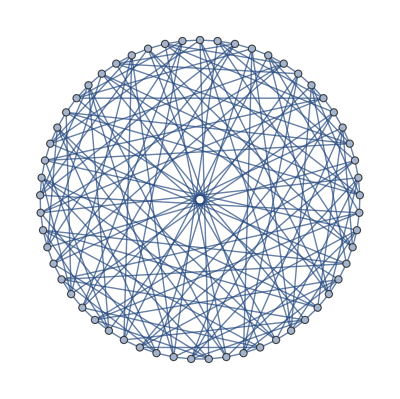

α(\bar G)=2, χ(G)=3

```mathematica
g=GraphData["PerkelGraph"]
gtest=GraphComplement@g;
(*Independence number of (\bar G) and chaomatic number of G*)
"α(\\bar G)="<>ToString[Length@@FindIndependentVertexSet@gtest]<>", χ(G)="<>
ToString@GraphData["PerkelGraph", "ChromaticNumber"]
```

Also, we know from SDP the Lovasz ϑ of Complement(Perkel) is ϑ(\bar G)=3

#### Drawing the Perkel graph

```mathematica
With[{conn=EdgeList[g],pos=Flatten[Table[{Sin[2π i/19]+2Sin[2 π k/3], Cos[2π i/19]+2Cos[2π k/3]}, {k, 3}, {i, 19}],1],posnum=Flatten[Table[{1.2Sin[2π i/19]+2Sin[2 π k/3], 1.2Cos[2π i/19]+2Cos[2π k/3]}, {k, 3}, {i, 19}],1]},
Graphics[{AbsolutePointSize[10], AbsoluteThickness->1,FontFamily->"Minion Pro", FontSize->12,
Gray, Line[{pos[[#[[1]]]], pos[[#[[2]]]]}]&/@conn, RGBColor[{0, 165, 180}/255], Point/@pos[[;;19]], RGBColor[{0, 85, 170}/255], Point/@pos[[20;;38]], Black, Point/@pos[[39;;]]
}, ImageSize->320]]
```

-Graphics-

```mathematica
With[{conn={{1,2},{1,3},{1,4},{1,5},{1,6},{1,10},{1,12},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,9},{2,11},{2,13},{2,16},{3,4},{3,7},{3,8},{3,10},{3,12},{3,13},{3,16},{4,7},{4,8},{4,9},{4,11},{4,14},{4,15},{5,6},{5,7},{5,8},{5,9},{5,12},{5,14},{5,16},{6,7},{6,8},{6,10},{6,11},{6,13},{6,15},{7,8},{7,10},{7,11},{7,14},{7,16},{8,9},{8,12},{8,13},{8,15},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{11,12},{11,15},{11,16},{12,15},{12,16},{13,14},{13,15},{13,16},{14,15},{14,16},{15,16}},pos=Flatten[Table[{Sin[2π (i+k/2)/4]+2.5Sin[2 π k/4], Cos[2π (i+k/2)/4]+2.5Cos[2π k/4]}, {k, .5, 3.5, 1}, {i, 4}],1]},
Graphics[{AbsolutePointSize[10], AbsoluteThickness->1, FontFamily->"Minion Pro", FontSize->12,
Black, Line[{pos[[#[[1]]]], pos[[#[[2]]]]}]&/@conn, RGBColor[{0, 165, 180}/255], Point/@pos[[;;4]], RGBColor[{0, 85, 170}/255], Point/@pos[[5;;8]], Black, Point/@pos[[9;;12]], Orange, Point/@pos[[13;;16]]
}, ImageSize->160]]
```

-Graphics-

```mathematica
With[{conn={{1,2},{2,3},{3,4},{4,5},{1,5}},pos=Table[{Sin[2π i/5],  Cos[2π i/5]}, {i, 5}]},
Graphics[{AbsolutePointSize[10], AbsoluteThickness->1, FontFamily->"Minion Pro", FontSize->12,
Black, Line[{pos[[#[[1]]]], pos[[#[[2]]]]}]&/@conn, RGBColor[{0, 165, 180}/255], Point/@pos[[{1, 2}]], RGBColor[{0, 85, 170}/255], Point/@pos[[{3,4}]], Black, Point/@pos[[{5}]]
}, ImageSize->80]]
```

-Graphics-

## Gram matrix of Complement(Perkel)

```mathematica
gmat={{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1/3,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0},{1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0},{0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3},{0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3},{1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0},{0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0},{1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0},{0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0},{0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0},{0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0},{0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,1/3},{0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/3,0,1/3,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1/3,1/3,0,0,0,0},{0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,1/3,0,0,0,1/3,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}};
MatrixRank[gmat]
```

37

We need 37-dimensional vectors to realize the orthogonal representation of \bar Perkel.

## Orthogonal representation of Complement(Perkel)

### Use Cholesky decomposition to obtain the first 37 linearly independent vectors

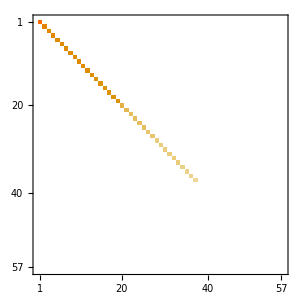
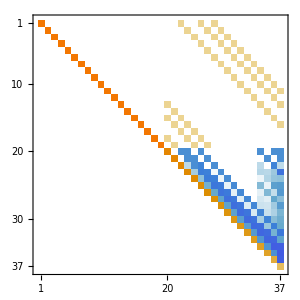

```mathematica
vec37=Normalize/@(CholeskyDecomposition[gmat[[;;37, ;;37]]]ᵀ);
{MatrixPlot[SingularValueDecomposition[N@gmat][[2]], ImageSize->300], MatrixPlot[vec37ᵀ, ImageSize->300]}
```

### Linear combination for the remaining 20 vectors

```mathematica
vec57=Join[vec37,Chop@
Table[Table[t[i], {i, 37}]/.Solve[(#.Table[t[i],{i, 37}])&@vec37==(gmat[[k,;;37]]), Table[t[i],{i, 37}]][[1]], {k, 38, 57}]];
```

We can check the set vec57 gives exactly the desired Gram matrix. Comparison:

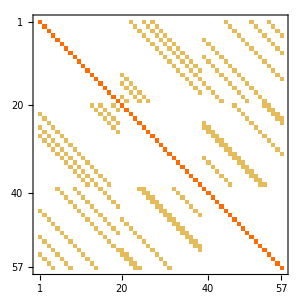
{-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[Chop@Outer[Dot, #, #, 1]&@vec57, ImageSize->300],
MatrixPlot[gmat, ImageSize->300]}
```

### Gram-Schmidt for orthonormal basis

```mathematica
gramsch[vecpool_]:=Module[{spanpool=Table[SparseArray[{1, k}->1, {1, 37}], {k, 20, 37}],raypool=N@vecpool},
For[k=1, k≤18, k++, 
vectemp=spanpool[[k, 1]]-Total[# First@Dot[spanpool[[k]], #]&/@raypool];
AppendTo[raypool, Normalize@vectemp]
];raypool
];
vec111=Chop@Join[gramsch[vec57[[1;;19]]],gramsch[vec57[[20;;38]]],gramsch[vec57[[39;;57]]]];
vec111//Dimensions
```

{111,37}

### The vectors themselves looks ugly but they should work! Every vector is represented in one column, rows correspond to vector entries

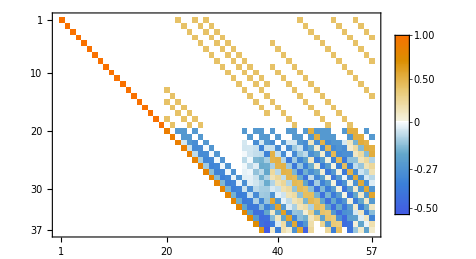

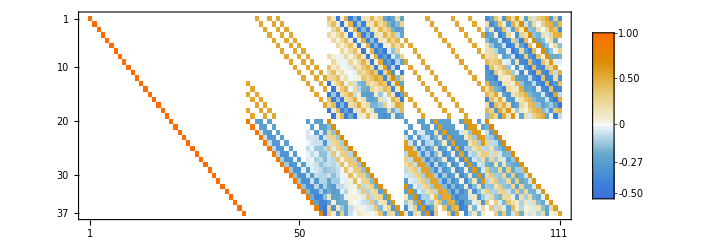

```mathematica
MatrixPlot[vec57ᵀ, ImageSize->400, PlotLegends->BarLegend[Automatic, LegendMarkerSize->200]]
MatrixPlot[vec111ᵀ, ImageSize->600, PlotLegends->BarLegend[Automatic, LegendMarkerSize->200]]
```

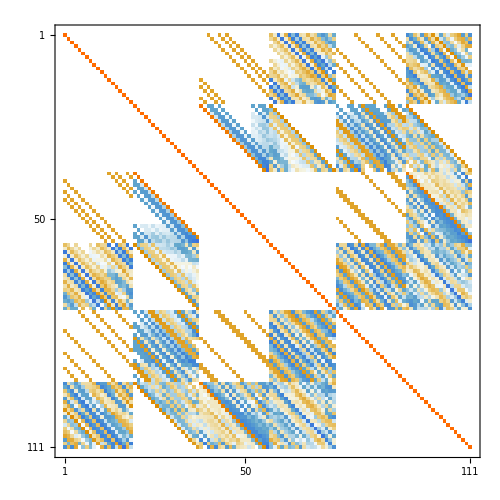

```mathematica
MatrixPlot[Chop@Outer[Dot, #, #, 1]&@N@vec111, ImageSize->500]
```

```mathematica
Chop[#.Join[Array[1/(√19)&, 19], Array[0&, 18]]&/@vec111]
```

{0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Partition into subspaces

```mathematica
vec42=Chop@Map[PadRight[#,7]&, {#[[1;;7]],#[[8;;14]],#[[15;;19]],#[[20;;25]],#[[26;;31]],#[[32;;37]]}&/@vec111, {2}];ortholist=Map[If[#≤19, #, If[#≥39, #+36, #+18]]&, EdgeList@gtest/.{x_<->y_:>{x,y}}, {2}];
prlv1=Chop@Join[Map[Dot[#,Table[1/(√19),7]]&, vec42[[;;, ;;3, ;;]], {2}], Map[Dot[#,Table[0, 7]]&, vec42[[;;, 4;;, ;;]], {2}],  2]
prlv2=Chop@Map[Dot[#,Table[1,6]]&, prlv1, {1}]
```

{{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0,0.229416,0,0,0},{0,0,0.229416,0,0,0},{0,0,0.229416,0,0,0},{0,0,0.229416,0,0,0},{0,0,0.229416,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0.0764719,0.152944,0,0,0},{0,0.0764719,0.152944,0,0,0},{0.0764719,0,0.152944,0,0,0},{0.0764719,0,0.152944,0,0,0},{0.0764719,0,0.152944,0,0,0},{0.152944,0,0.0764719,0,0,0},{0.152944,0,0.0764719,0,0,0},{0.229416,0,0,0,0,0},{0.229416,0,0,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.0764719,0.152944,0,0,0,0},{0.0764719,0.152944,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.229416,0,0,0,0},{0,0.152944,0.0764719,0,0,0},{0,0.152944,0.0764719,0,0,0},{0,0.152944,0.0764719,0,0,0},{0.0883022,0.0220755,-0.110378,0,0,0},{0.104481,0.0261201,-0.130601,0,0,0},{0.00897013,0.114369,-0.123339,0,0,0},{0.00598659,0.10453,-0.110516,0,0,0},{0.0451997,0.0947904,-0.13999,0,0,0},{-0.0394899,0.0417695,-0.00227961,0,0,0},{-0.0780942,0.0652417,0.0128525,0,0,0},{-0.192693,0.0949727,0.0977205,0,0,0},{-0.18132,0.123351,0.0579687,0,0,0},{-0.0712219,0.0516492,0.0195727,0,0,0},{-0.0175517,0.0814963,-0.0639446,0,0,0},{-0.0732418,0.133458,-0.0602161,0,0,0},{0.0162595,0.0753355,-0.091595,0,0,0},{0.00915303,0.0530334,-0.0621865,0,0,0},{0.0589763,-0.0854859,0.0265096,0,0,0},{0.0260361,-0.0926818,0.0666457,0,0,0},{0.0563152,-0.0187339,-0.0375813,0,0,0},{0,0.0265338,-0.0265338,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0,0.152944,0.0764719,0,0,0},{0,0.152944,0.0764719,0,0,0},{0.0764719,0.152944,0,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0,0.152944,0,0,0},{0.152944,0,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.0764719,0.0764719,0.0764719,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.152944,0.0764719,0,0,0,0},{0.0764719,0.152944,0,0,0,0},{-0.0720984,0.0180246,0.0540738,0,0,0},{-0.121869,0.021327,0.100542,0,0,0},{-0.118903,-0.0100887,0.128992,0,0,0},{-0.131684,0.00754269,0.124141,0,0,0},{-0.135433,-0.000340992,0.135774,0,0,0},{-0.0967916,0.043316,0.0534756,0,0,0},{-0.0555075,0.0145065,0.0410011,0,0,0},{0.0829449,-0.0724119,-0.0105329,0,0,0},{0.0724211,-0.137783,0.0653617,0,0,0},{0.0470102,-0.182264,0.135253,0,0,0},{0.0775185,-0.188498,0.11098,0,0,0},{0.142477,-0.230371,0.0878937,0,0,0},{0.112832,-0.150765,0.0379336,0,0,0},{0.162199,-0.146179,-0.01602,0,0,0},{0.102618,0.00678194,-0.1094,0,0,0},{0.119409,0.0643467,-0.183755,0,0,0},{0.105491,-0.0315566,-0.0739341,0,0,0},{0.0301595,-0.0217819,-0.00837764,0,0,0}}

{0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0.229416,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ortholist=Map[If[#≤19, #, If[#≤38, #+18, #+36]]&, Position[gmat, 0], {2}];
erlv0=Chop@Table[vec42[[ortholist[[k, 1]]]]*vec42[[ortholist[[k, 2]]]], {k, Length@ortholist}];
erlv1=Map[Total, Chop@Table[vec42[[ortholist[[k, 1]]]]*vec42[[ortholist[[k, 2]]]], {k, Length@ortholist}], {2}];
erlv2=Chop/@Total/@erlv1;
Dimensions@erlv0
Tally[erlv2]
```

{2850,6,7}

{{0,2850}}

## Dispersion and homodyne efficiency

```mathematica
δλ0=6*^-9;
Exp[-x^2/(δλ0^2/Log[2])]/.x->(6.*^-9)
```

0.5

Pulse in time domain is ps wide

```mathematica
((1560.*^-9)^2)/(3*^8*δλ0)//ScientificForm
```

1.352×10^-12

Pulse in spatial domain have 0.4 mm coherence length

```mathematica
l0=((1560.*^-9)^2)/δλ0; l0//ScientificForm
```

4.056×10^-4

Length of fiber in small loop is roughly 8 m

```mathematica
δL=(3*^8)/(75.914*^6)*3/1.468
```

8.07597

Estimated coherence length growth per round trip

```mathematica
δl=17*^-6*δL*δλ0*3*^8; δl//ScientificForm
```

2.47125×10^-4

#### Wavefunction overlapping incl. 20 μm misalignment, 80% loop efficiency, and dispersion in both signal/LO

```mathematica
δλ[n_]:=((1560.*^-9)^2)/(l0+(n+3)δl);
δλcorr[m_, n_]:=(∫_(-∞)^(+∞) Exp[-x^2/(2*δλ[m]^2/Log[2])]Exp[-((x-n δλ0 *(2*^-5)/l0 )^2)/(2*δλ[n]^2/Log[2])]ⅆx)/(√(∫_(-∞)^(+∞) Exp[-x^2/(δλ[m]^2/Log[2])]ⅆx)√(∫_(-∞)^(+∞) Exp[-x^2/(δλ[n]^2/Log[2])]ⅆx));
r=.794;
eff=#/(First@#)&@Table[Re@δλcorr[k, 5]*r^k, {k, 12}]
```

{1.,0.783058,0.605815,0.465417,0.356242,0.272259,0.208038,0.159069,0.121764,0.0933383,0.0716563,0.0550953}

## Electronic pulse

```mathematica
genMajorSeq[x_]:=Module[{sorted=Sort[x, Abs[#1]<Abs[#2]&]},
{sorted, Flatten[Position[x, #]&/@DeleteDuplicates@sorted, 2]}
];
genMajorSeq[{1, 4, 2, 2, -3, 7}]
```

{{1,2,2,-3,4,7},{1,3,4,5,2,6}}

```mathematica
statelistlv1=(Tally@Flatten[Map[genMajorSeq, vec42, {2}][[;;, ;;, 1]], 1])[[;;, 1]]; Length@statelistlv1
stateposlv1=Map[Position[statelistlv1, #]&, (Map[genMajorSeq, vec42, {2}][[;;, ;;, 1]]), {2}][[;;, ;;, 1, 1]]
```

277

{{1,2,2,2,2,2},{1,2,2,2,2,2},{1,2,2,2,2,2},{1,2,2,2,2,2},{1,2,2,2,2,2},{1,2,2,2,2,2},{1,2,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,1,2,2,2,2},{2,2,1,2,2,2},{2,2,1,2,2,2},{2,2,1,2,2,2},{2,2,1,2,2,2},{2,2,1,2,2,2},{2,2,2,1,2,2},{2,2,2,1,2,2},{2,2,2,1,2,2},{2,2,2,1,2,2},{2,2,2,1,2,2},{2,2,2,1,2,2},{2,2,2,2,1,2},{2,2,2,2,1,2},{2,2,2,2,1,2},{2,2,2,2,1,2},{2,2,2,2,1,2},{2,2,2,2,1,2},{2,2,2,2,2,1},{2,2,2,2,2,1},{2,2,2,2,2,1},{2,2,2,2,2,1},{2,2,2,2,2,1},{2,2,2,2,2,1},{2,3,4,5,2,2},{2,3,4,5,2,2},{3,2,4,6,2,2},{3,2,4,7,2,2},{3,2,4,8,2,2},{4,2,3,9,2,2},{4,2,3,10,11,2},{12,2,2,13,14,2},{12,2,2,15,16,2},{4,3,2,17,18,2},{4,3,2,19,20,2},{4,3,2,2,21,2},{3,4,2,2,22,23},{3,4,2,2,24,25},{2,12,2,26,27,28},{2,12,2,29,30,31},{2,4,3,32,33,34},{2,4,3,35,36,37},{2,4,3,38,39,40},{41,42,43,44,45,46},{47,48,49,50,51,52},{53,54,55,56,57,58},{59,60,61,62,63,64},{65,66,67,68,69,70},{71,72,73,74,75,76},{77,78,79,2,80,81},{82,83,84,2,85,86},{87,88,89,2,90,91},{92,93,94,2,95,96},{97,98,99,2,100,101},{102,103,104,2,105,106},{107,108,109,2,2,110},{111,112,113,2,2,114},{115,116,117,2,2,118},{119,120,121,2,2,122},{123,124,125,2,2,126},{127,128,129,2,2,130},{3,3,3,131,132,133},{3,3,3,134,135,136},{3,3,3,137,138,139},{2,4,3,140,141,142},{2,4,3,143,144,145},{3,4,2,146,147,148},{3,3,3,149,150,151},{3,3,3,152,153,154},{3,3,3,155,156,157},{3,3,3,158,159,160},{3,2,4,161,162,163},{4,2,3,164,165,166},{3,3,3,167,168,169},{3,3,3,170,171,172},{3,3,3,173,174,175},{4,3,2,176,177,178},{4,3,2,179,180,181},{4,3,2,182,183,184},{3,4,2,185,186,187},{188,189,190,191,192,193},{194,195,196,197,198,199},{200,201,202,203,204,205},{206,207,208,209,210,211},{212,213,214,215,216,217},{218,219,220,221,222,223},{224,225,226,2,227,228},{229,230,231,2,232,233},{234,235,236,2,237,238},{239,240,241,2,242,243},{244,245,246,2,247,248},{249,250,251,2,252,253},{254,255,256,2,2,257},{258,259,260,2,2,261},{262,263,264,2,2,265},{266,267,268,2,2,269},{270,271,272,2,2,273},{274,275,276,2,2,277}}

```mathematica
pulselistlv1=#/Reverse[eff[[;;7]]]&/@statelistlv1;
Max@pulselistlv1
```

1.

```mathematica
statelistlv2=(Tally@Map[genMajorSeq, Join[#, {0}]&/@prlv1, {1}][[;;, 1]])[[;;, 1]]; Length@statelistlv2
stateposlv2=Map[Position[statelistlv2, #]&, Map[genMajorSeq, Join[#, {0}]&/@prlv1, {1}][[;;, 1]]]//Flatten
```

40

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,1,1,3,3,3,3,3,1,1,3,3,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,22,22,3,3,3,22,22,22,22,3,3,22,22,22,3,3,3,3,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
pulselistlv2=#/Reverse[eff[[;;7]]]&/@statelistlv2;
Max@pulselistlv2
pulselistlv2=#/Max@#&@pulselistlv2;
Max@pulselistlv2
```

0.229416

1.

```mathematica
errpool=Chop@Table[vec42[[ortholist[[k, 1]]]]*vec42[[ortholist[[k, 2]]]], {k, Length@ortholist}];
errlist=(Tally@Flatten[Map[genMajorSeq, errpool, {2}][[;;, ;;, 1]], 1])[[;;, 1]]; Length@errlist
errpos=Map[Position[Round[errlist, 1.*^-6], #]&, Map[genMajorSeq, Round[errpool, 1.*^-6], {2}][[;;, ;;, 1]], {2}][[;;, ;;, 1, 1]]
```

1199

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},2829,{2,1,1,1062,1063,1064},{1,2,1,1089,1090,1091},{1,1,1,1113,1114,1115},{1,1,1,1134,1135,1136},{1,2,1,1152,1153,1154},{1,1,1,1167,1168,1169},{2,1,1,1179,1180,1181},{1,1,1,1188,1189,1190},{1,1,1,1194,1195,1196},{1,1,1,1197,1198,1199}}
 |  |  |  |

```mathematica
pulseerr=#/Reverse[eff[[;;7]]]&/@errlist;
Max@pulseerr
```

0.166667

## Generate AFG waveform

```mathematica
volIM[pulse_]:=Join[Table[1, 15], {-1}, Table[1, 9], Table[0, 13], pulse, Table[0, 10], Table[1, 15]];
volPM[]:=Join[Table[-.9, 22], Table[.9, 10], Table[-.9, 38]];impulse=SetPrecision[#, 5]&/@volIM/@Join[pulselistlv1, pulselistlv2, pulseerr];
pmpulse=SetPrecision[#, 5]&/@Table[volPM[], {k, Length@impulse}];
```

```mathematica
Export["impulse.txt", impulse, "Table"]
Export["pmpulse.txt", pmpulse, "Table"]
```

impulse.txt

pmpulse.txt

## Electronic pulse representation

```mathematica
<<MaTeX`;
SetOptions[MaTeX, FontSize->28];
SetOptions[MaTeX, "Preamble"->{"\\usepackage{xcolor}", "\\definecolor{mathorange}{rgb}{0.9728, 0.6216, 0.0734}", "\\definecolor{mathgreen}{rgb}{0.5602, 0.6916, 
 0.1949}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor},\definecolor{mathorange}{rgb}{0.9728, 0.6216, 0.0734},\definecolor{mathgreen}{rgb}{0.5602, 0.6916, 
 0.1949}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→28,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
samplepulse=Join[{0}, SetPrecision[pulselistlv1[[112]], 3], {0}]
samplewaveraw=Flatten@Import["E:\\GooglePlex\\Codes\\Mathematica\\2205 PerkelContext\\raw\\samplewave.txt", "Table"];
samplewave=ArrayResample[ListConvolve[Table[1, 99], samplewaveraw][[2750;;8000]], 1601]+940;
```

{0,0.54,-0.481,0.441,0.501,-0.417,-0.352,0.387,0}

```mathematica
Graphics[{AbsoluteThickness[2], EdgeForm[None], FontFamily->"MinionPro", FontSize->28,
(*Area*)
LightGray, Cuboid[{-10, -48}, {0, 48}], Cuboid[{120, -48}, {150, 48}],
Darker@Gray, Cuboid[{119, -26}, {121, -18}], Arrowheads[.03], Arrow[Line[{{120, -22}, {136, -22}}]],  
(*Sample Osc waveform*)
RGBColor[{0, 105, 169}/255],
{CapForm["Round"], Table[Line[{{(k-1)/10-10, Min[samplewave[[k]]/15, 48]}, {k/10-10, Min[samplewave[[k+1]]/15, 48]}}], {k, Length@samplewave-1}]},
{Opacity[.3], (*Table[Cuboid[{(k-1)/10-10, Min[samplewave[[k]]/15, 48]}, {k/10-10, 0}], {k, Length@samplewave-1}]*)
Polygon@Join[{{-10, 0}}, Table[{k/10-10, Min[samplewave[[k]]/15, 48]}, {k, Length@samplewave}], {{150, 0}, {-10, 0}}]},
(*Right edge for PM*)
ColorData[97, 3], Line[{{150, -48}, {150, 48}}],
Table[Line[{{150, y}, {148, y}}], {y, -30, 30, 60}],
(*Rotate[Text[MaTeX["\\color{mathgreen} \\text{PM phase}"], {168, 2}],   -π/2],
Text[MaTeX["\\color{mathgreen} \\frac{\\pi}{2}"], {158, 30}],
Text[MaTeX["\\color{mathgreen} 0"], {158, -30}],*)
Rotate[Text["PM phase", {168, 0}], -π/2],
Text[MaTeX["\\color{mathgreen} \\frac {\\pi}{2}"], {158, 30}],
Text[0, {158, -30}],
(*PM pulse*)
Line[{{-10, -30}, {21, -30}, {21, 30}, {51, 30}, {51, -30}, {150, -30}}],
(*Left edge for IM*)
ColorData[97, 13], Line[{{-10, -48}, {-10, 48}}],
Table[Line[{{-10, y}, {-8, y}}], {y, -40, 40, 40}],
(*Rotate[Text[MaTeX["\\color{mathorange} \\text {IM voltage\\;/\\;a.u.}"], {-30, 4}], π/2],
Text[MaTeX["\\color{mathorange} 1"], {-18, 34}, {1, 0}],
Text[MaTeX["\\color{mathorange} 0"], {-18, -6}, {1, 0}],
Text[MaTeX["\\color{mathorange} -1"], {-24, -44}, {1, 0}],*)
Rotate[Text["IM voltage / a.u.", {-30, 4}], π/2],
Text["1", {-14, 40}, {1, 0}],
Text["0", {-14, 0}, {1, 0}],
Text["-1", {-14, -40}, {1, 0}],
(*IM pulse*)
Line[{{-10, 40}, {0, 40}, {0, -40}, {3, -40}, {3, 40}, {30, 40}, {30, 0}, {67.5, 0}}],
Table[Line[{{{64.5+3k, 40samplepulse[[k]]}, {66+3k, 40samplepulse[[k]]}}, {{66+3k, 40samplepulse[[k]]}, {66+3k, 40samplepulse[[k+1]]}}, {{66+3k, 40samplepulse[[k+1]]}, {67.5+3k, 40samplepulse[[k+1]]}}}], {k, -1+Length@samplepulse}],
Line[{{91.5, 0}, {120, 0}, {120, 40}, {150, 40}}],
(*UP/BOTTOM*)
{Black, FontSize->20,Text["98.5 μs", {136, -15}],Text["lock", {135, -7}]},
Black, Line[{{{-10, -48}, {150, -48}}, {{-10, 48}, {150, 48}}}], 
Table[Line[{{x, -48}, {x, -47}}], {x, -8, 148, 2}],
Table[Line[{{x, -48}, {x, -46}}], {x, 0, 140, 10}],
Text["Time / μs", {70, -67}],
Table[Text[ToString[.5k], {40k, -49}, {0, 1}], {k, 0, 3}]
}, ImageSize->600]
```

-Graphics-

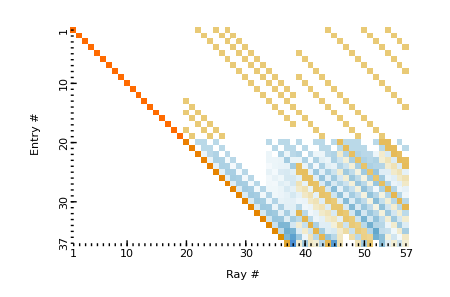

```mathematica
With[{vec57n=1/2+vec57/2, cfun=Blend[{{0.,RGBColor[0.260487,0.356,0.891569]},{0.166667,RGBColor[0.230198,0.499962,0.848188]},{0.333333,RGBColor[0.392401,0.658762,0.797589]},{0.499999,RGBColor[0.964837,0.982332,0.98988]},{0.5,RGBColor[1,1,1]},{0.500001,RGBColor[0.95735,0.957281,0.896269]},{0.666667,RGBColor[0.913252,0.790646,0.462837]},{0.833333,RGBColor[0.860243,0.558831,0.00695811]},{1.,RGBColor[1.,0.42,0.]}},#1]&}, 
Graphics[{EdgeForm[None], AbsoluteThickness[2], CapForm["Round"], JoinForm["Round"], FontSize->20, FontFamily->"Minion Pro",
Table[{cfun[vec57n[[j, k]]], Cuboid[{j-1, 37-k}, {j, 38-k}]}, {j, 57}, {k, 37}],
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{0, 0}, {57, 37}]},
AbsoluteThickness[1], Table[Line[{{k-.5, 0}, {k-.5, .5}}], {k, 57}], Table[Line[{{k-.5, 0}, {k-.5, 1}}], {k, 10, 50, 10}], 
Table[Line[{{0, k-.5}, {.5, k-.5}}], {k, 37}], 
Table[Line[{{0, k-.5}, {1, k-.5}}], {k, 28, 8, -10}],
Text["Ray #", {29, -4}, {0, 1}], Text["Entry #", {-5, 19}, {0, -1}, {0, 1}],
Text[ToString@#, {#-.5, -.5}, {0, 1}]&/@{1, 10, 20, 30, 40, 50, 57},
Text[ToString@#, {-.3, 37.5-#}, {0, -1}, {0, 1}]&/@{1, 10, 20, 30, 37}, 
}, ImageSize->450]]
```

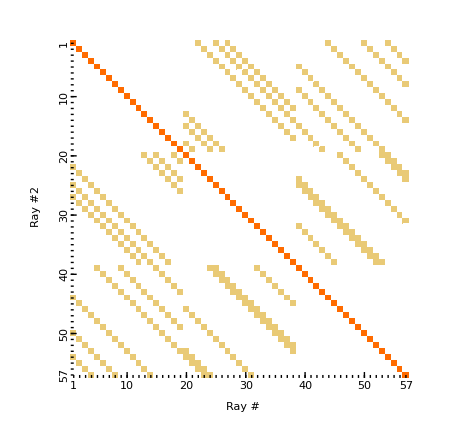

```mathematica
With[{gmatn=1/2+gmat/2, cfun=Blend[{{0.,RGBColor[0.260487,0.356,0.891569]},{0.166667,RGBColor[0.230198,0.499962,0.848188]},{0.333333,RGBColor[0.392401,0.658762,0.797589]},{0.499999,RGBColor[0.964837,0.982332,0.98988]},{0.5,RGBColor[1,1,1]},{0.500001,RGBColor[0.95735,0.957281,0.896269]},{0.666667,RGBColor[0.913252,0.790646,0.462837]},{0.833333,RGBColor[0.860243,0.558831,0.00695811]},{1.,RGBColor[1.,0.42,0.]}},#1]&}, 
Graphics[{EdgeForm[None], AbsoluteThickness[2], CapForm["Round"], JoinForm["Round"], FontSize->20, FontFamily->"Minion Pro",
Table[{cfun[gmatn[[j, k]]], Cuboid[{j-1, 57-k}, {j, 58-k}]}, {j, 57}, {k, 57}],
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{0, 0}, {57, 57}]},
AbsoluteThickness[1], Table[Line[{{k-.5, 0}, {k-.5, .5}}], {k, 57}], Table[Line[{{k-.5, 0}, {k-.5, 1}}], {k, 10, 50, 10}], 
Table[Line[{{0, k-.5}, {.5, k-.5}}], {k, 57}], 
Table[Line[{{0, k-.5}, {1, k-.5}}], {k, 48, 8, -10}],
Text["Ray #", {29, -4}, {0, 1}], Text["Ray #2", {-5, 29}, {0, -1}, {0, 1}],
Text[ToString@#, {#-.5, -.5}, {0, 1}]&/@{1, 10, 20, 30, 40, 50, 57},
Text[ToString@#, {-.3, 57.5-#}, {0, -1}, {0, 1}]&/@{1, 10, 20, 30, 40, 50, 57}, 
}, ImageSize->450]]
```

```mathematica
With[{cfun=Blend[{{0.,RGBColor[0.260487,0.356,0.891569]},{0.166667,RGBColor[0.230198,0.499962,0.848188]},{0.333333,RGBColor[0.392401,0.658762,0.797589]},{0.499999,RGBColor[0.964837,0.982332,0.98988]},{0.5,RGBColor[1,1,1]},{0.500001,RGBColor[0.95735,0.957281,0.896269]},{0.666667,RGBColor[0.913252,0.790646,0.462837]},{0.833333,RGBColor[0.860243,0.558831,0.00695811]},{1.,RGBColor[1.,0.42,0.]}},#1]&}, 
Graphics[{EdgeForm[None], AbsoluteThickness[2], CapForm["Round"], JoinForm["Round"], FontSize->20, FontFamily->"Minion Pro",

{Table[{cfun[k/99], Cuboid[{63, 2.7+.3k}, {65, 3+.3k}]}, {k, 100}]},
{EdgeForm[{Black, AbsoluteThickness[2]}], Transparent, Cuboid[{63, 3}, {65, 33}]},
Table[Line[{{65, 3+1.5k}, {64.5, 3+1.5k}}], {k, 19}], Text[ToString@#, {66.5, 18+15#}, {-1, 0}]&/@{1., .5, 0., -.5, -1.}
}, ImageSize->60]]
```

-Graphics-